```mathematica
SetDirectory[NotebookDirectory[]];
Needs["VectorFieldPlots`"];
p=ReadList["Out_SK2.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];
L=7;

Dimensions[p]
p=ArrayReshape[p,{L,L,32}];
L*L*32
Dimensions[p]
```

{1568,1}

1568

{7,7,32}

```mathematica
For[i=1,i≤32,i++,
Export[ToString[i]<>".png",ListContourPlot[p[[All,All,i]],FrameTicksStyle->Directive[FontOpacity->0,FontSize->0], ContourStyle->None,InterpolationOrder->2]]]
```

```mathematica
coord =Flatten[Table[{x,y},{x,1,L,1},{y,1,L,1}],1];
CONFnewlist=Table[{{coord[[i]][[1]],coord[[i]][[2]],0},Flatten[p,1][[i]]},{i,L*L}];
ListVectorFieldPlot3D[CONFnewlist,ScaleFactor->1,VectorHeads->True]
```

-Graphics3D-

{512,1}

1L5.png

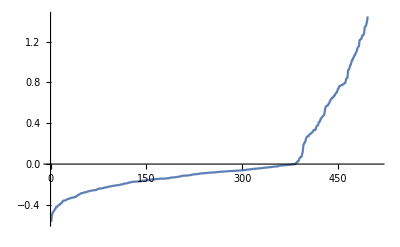

```mathematica
p=ReadList["Out_SK4.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];
Dimensions[p]
Export["1L5.png",ListLinePlot[Sort[Flatten[p]],BaseStyle->{FontSize->18, FontWeight->Bold}]]
ListLinePlot[Sort[Flatten[p]],BaseStyle->{FontSize->18, FontWeight->Bold}]
```